```mathematica
(*Data*)
Get["RootSearch`"]
nperiods = 2400;
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;
τ = 0;


period = 2 π √(a^3/μ);
ranget = nperiods*period;

psiQ =τ Cos[α[t]] Cos[γ[t]] ;
alphaQ =τ Sin[γ[t]];

(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{γ'[t]+(θ'[t]+ψ'[t])Sin[α[t]]}, {-Cos[γ[t]] α'[t]+Cos[α[t]] Sin[γ[t]] (θ'[t]+ψ'[t])}, {Sin[γ[t]] α'[t]+Cos[α[t]] Cos[γ[t]] (θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2=Simplify[D[D[L, α'[t]], t]-D[L, α[t]]-alphaQ];
eqn3 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn4 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];
eqn5 = Cos[α[t]] α'[t] (θ'[t]+ψ'[t])+γ''[t]+Sin[α[t]] (θ''[t]+ψ''[t]);
```

```mathematica
motorisedBiffunc[e_]:=(
alpha0 = 0.5;
alphadsh0 = 0 ;
psi0 = 0;
psidsh0 =0;
gamma0=0;
r0 = a (1-e);
rdsh0 = 0;
theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;
system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,eqn4==0,eqn5==0,
α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0,γ[0]==gamma0,γ'[0]==-(thetadsh0+psidsh0)Sin[alpha0]},
{ψ,α,θ,rc,γ},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->10];
psis[t_]:=ψ[t]/.system[[1]];
psidhs[t_]:=ψ'[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
gammas[t_]:=γ[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
rvs[t_]:=rc'[t]/.system[[1]];
)
```

```mathematica
motorisedBiffunc[0.0711]
```

```mathematica
rootst = {};
Do[Print[n];rootst = Append[rootst,RootSearch[rvs[t]==0,{t,period*n,(n+20)*period}]],{n,0,nperiods-21,20}];
rootst = Flatten[rootst];
```

0

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

20

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

40

$MinPrecision::precset: Cannot set $MinPrecision to -∞; value must be a non-negative number or Infinity.

General::stop: Further output of $MinPrecision::precset will be suppressed during this calculation.

60

80

100

120

140

160

180

200

220

240

260

280

300

320

340

360

380

400

420

440

460

480

500

520

540

560

580

600

620

640

660

680

700

720

740

760

780

800

820

840

860

880

900

920

940

960

980

1000

1020

1040

1060

1080

1100

1120

1140

1160

1180

1200

1220

1240

1260

1280

1300

1320

1340

1360

1380

1400

1420

1440

1460

1480

1500

1520

1540

1560

1580

1600

1620

1640

1660

1680

1700

1720

1740

1760

1780

1800

1820

1840

1860

1880

1900

1920

1940

1960

1980

2000

2020

2040

2060

2080

2100

2120

2140

2160

2180

2200

2220

2240

2260

2280

2300

2320

2340

2360

```mathematica
roots = {};
Do[roots = Append[roots,t/.rootst[[n]]],{n,1,Length[rootst]}];
rvals = {};
Do[rvals = Append[rvals,{roots[[n]],rs[roots[[n]]]}],{n,1,Length[roots]}]
peris = Select[rvals,#[[2]]<6.6*10^6&];
apos = Select[rvals,#[[2]]>6.6*10^6&];
psips = {};
psias = {};
Do[psips = Append[psips,{psis[peris[[n]][[1]]],psidhs[peris[[n]][[1]]]}],{n,1,Length[peris]}]
Do[psias = Append[psias,{psis[apos[[n]][[1]]],psidhs[apos[[n]][[1]]]}],{n,1,Length[apos]}]
```

RootSearch::shdw: Symbol RootSearch appears in multiple contexts {Ersek`RootSearch`,Global`}; definitions in context Ersek`RootSearch` may shadow or be shadowed by other definitions.

2379

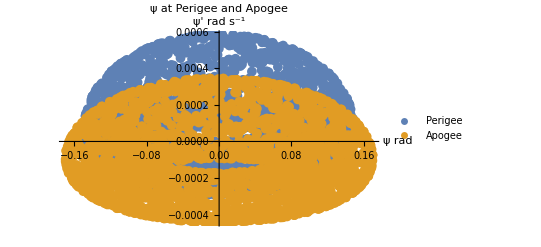

```mathematica
Length[psips]
ListPlot[{psips,psias},PlotMarkers->{•,10},PlotLabel->Style["ψ at Perigee and Apogee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["ψ rad",FontFamily->"Liberation Serif"],Style["ψ' rad s^-1",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{1080},PlotLegends->{"Perigee","Apogee"}]
```

```mathematica
rvs[period*20000]
```

-480.376

```mathematica
Anime =Table[ListPlot[{psips[[start;;start+100]],psias[[start;;start+100]]},PlotMarkers->{•,10},PlotLabel->Style["ψ at Perigee and Apogee",FontFamily->"Liberation Serif",35],AxesLabel->{Style["e",FontFamily->"Liberation Serif"],Style["ψ(θ_p) rad",FontFamily->"Liberation Serif"]},LabelStyle->Directive[Black,18,FontFamily->"Liberation Serif"],ImageSize->{500},PlotRange->{{-0.05,0.05},{-0.0002,0.0002}},PlotLegends->{"Perigee","Apogee"}],{start,1,2280,1}];
```

```mathematica
Export["wigglyworms.avi",Anime]
```

wigglyworms.avi